```mathematica
f[δ_,r_,Θ_,t1_]:=Cos[Θ]*Sin[Θ]*(t1^2*r^2*Sin[δ])/((1-r^2)^2+4*r^2*Sin[δ/2]^2)
```

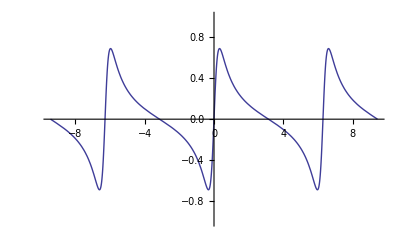

```mathematica
Plot[f[δ,0.85,1,1],{δ,-3*Pi,3*Pi}, PlotRange-> {-1,1}]
```